# Vaje iz Mathematice, 1. del

### 1. naloga:

Izračunaj vrednost izraza  ((20+316)^7-55)/(33·12)^3

Izračunaj še numerično vrednost istega izraza na 20 mest natančno.

```mathematica
((20+316)^7-55)/(33 12)^3
```

483476023799709641/62099136

```mathematica
N[((20+316)^7-55)/(33 12)^3,20]
```

7.7855515381036805568×10^9

### 2. naloga:

Poenostavi izraz  2^x+5a 2^x+2^(x+2)

```mathematica
Simplify[2^x+5 a 2^x+2^(x+2)]
```

5 2^x (1+a)

### 3. naloga:

Poišči največji skupni delitelj števil 536, 1248, 2320.

Poišči še najmanjši skupni večkrat teh števil.

```mathematica
l={536, 1248, 2320}
```

{536,1248,2320}

```mathematica
Apply[GCD,l]
```

8

```mathematica
LCM@@l
```

12124320

### 4. naloga:

Seštej vsa soda števila na intervalu [1,100].

```mathematica
∑_(x=1)^50 2 x
```

2550

### 5. naloga:

Izračunaj  ∑_(k=1)^∞ (k^2+1)/k^4

```mathematica
∑_(k=1)^∞ (k^2+1)/k^4
```

1/90 π^2 (15+π^2)

### 6. naloga:

Izračunaj vrednost izraza (sin α + sin β)/(cos^2(α - β) - sin^2(β-α)) za kota α=1830°  in  β=270°.

```mathematica
(Sin[α]+Sin[β])/(Cos[α-β]^2-Sin[β-α]^2)/.{α->1830 °,β->270 °}
```

1

### 7. naloga:

Izračunaj vrednost izraza  (x^5-2 x^2+3x+4)/(x^5-2x-1)  pri x=1, 2, ..., 10. 
Uporabi transformacijsko pravilo in ukaz  ReplaceAll  oz.  /.

Isto nalogo reši še s pomočjo ukaza Table.

```mathematica
(x^5-2 x^2+3 x+4)/(x^5-2 x-1)/.{x->Range[10]}
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
(x^5-2 x^2+3 x+4)/(x^5-2 x-1)/.{x->Table[i,{i,10}]}
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

### 8. naloga:

Dan je pravilen šestkotnik s stranico r. Kolikšna je ploščina kolobarja, ki ga določata včrtana in očrtana krožnica?

```mathematica
π (r^2-((√3 r)/2)^2)
```

(π r^2)/4

### 9. naloga:

Sin je 3 leta starejši od hčere, mati pa je 23 let starejša od sina. Pred 6 leti je imela mati 4 krat toliko let kot sin in hči skupaj. Koliko je star vsak od njih?

```mathematica
Solve[{sin==hci+3,mati==sin+23,mati-6==4 (sin-6+hci-6)}]
```

{{hci→8,mati→34,sin→11}}

### 10. naloga:

Poišči vsa kompleksna števila, ki zadoščajo enačbi  z̄=z^2

```mathematica
Solve[Conjugate[z]==z^2]
```

{{z→0},{z→1},{z→-1/2-(ⅈ √3)/2},{z→-1/2+(ⅈ √3)/2}}

### 11. naloga:

Koliko začetnih členov zaporedja s splošnim členom  a_n=16-2n  moramo sešteti, da bo vsota enaka 36?

```mathematica
Solve[∑_(n=1)^N (16-2 n)==36]
```

{{N→3},{N→12}}

### 12. naloga:

Dokaži, da je x=1 rešitev enačbe  a x^2-2b x+c=0, če a, b in c sestavljajo aritmetično zaporedje.

```mathematica
a x^2-2 b x+c==0/.{x->1,a->b-d,c->b+d}
```

True

### 13. naloga:

Določi vrednost parametra a v enačbi (2a x+3a)/(3a + 5x)=(3a-4)/(3a + 5x), da bo  x=2  rešitev enačbe.

```mathematica
Solve[(2 a x+3 a)/(3 a+5 x)==(3 a-4)/(3 a+5 x)/.{x->2}]
```

{{a→-1}}

### 14. naloga:

Na kakšne načine lahko plačamo poštnino 2,27 EUR z znamkami za 10, 23 in 37 centov?

```mathematica
Grid[Solve[{a 10+b 23+c 37==227,a≥0,b≥0,c≥0},{a,b,c},Integers]]
```

a→1 | b→3 | c→4
a→2 | b→9 | c→0
a→7 | b→2 | c→3
a→13 | b→1 | c→2
a→19 | b→0 | c→1

### 15. naloga:

Poišči štirimestno število, ki je popoln kvadrat in katerega prvi dve števki sta med seboj enaki, drugi dve pa prav tako med seboj enaki.

```mathematica
Solve[{c==a 10^3+a 10^2+10 b+b,0<a≤9,b≤9,√c==Round[√c]},]
```

{{a→7,b→4,c→7744}}

### 16. naloga:

Na kocko s stranico a postavimo drugo kocko s telesno diagonalo, enako stranici prve kocke, na drugo kocko spet tretjo s telesno diagonalo, enako stranici druge kocke, in to ponavljamo brez konca. Izračunaj višino tako dobljenega telesa.

Izračunaj še prostornino tako dobljenega telesa.

```mathematica
FullSimplify[∑_(n=0)^∞ a ((√3)/3)^n]
```

1/2 (3+√3) a

```mathematica
FullSimplify[∑_(n=0)^∞ (a ((√3)/3)^n)^3]
```

3/26 (9+√3) a^3

### 17. naloga:

Določi premico y=k x+n, ki gre skozi točki (-2,3) in (6,-1).

Nariši dobljeno premico na intervalu [-3,7] tako, da bosta enoti na koordinatnih oseh enako veliki.
Na sliki označi še točki, skozi kateri poteka premica.

```mathematica
sol=Solve[{3==k (-2)+n,-1==k 6+n},{k,n}]
```

{{k→-1/2,n→2}}

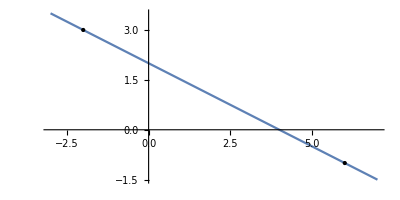

```mathematica
p=Plot[k x+n/.sol,{x,-3,7},AspectRatio->Automatic];
g=Graphics[{{PointSize[Large],Point[{-2,3}]},{PointSize[Large],Point[{6,-1}]}}];
Show[p,g]
```

### 18. naloga:

Določi inverzno funkcijo funkcije  y=2ln(3x-1)

Nariši grafa obeh funkcij v istem koordinatnem sistemu.

```mathematica
InverseFunction[2 Log[3 #1-1]&]
```

ConditionalExpression[1/3 (1+ⅇ^(#1/2)),-2 π<Im[#1]≤2 π]&

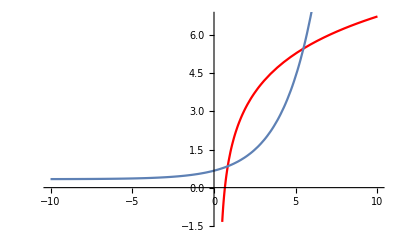

```mathematica
Show[Plot[2 Log[3 x-1],{x,-10,10},PlotStyle->Red],Plot[InverseFunction[2 Log[3 #1-1]&][x],{x,-10,10}]]
```